```mathematica
Clear[Evaluate[Context[]<>"*"]];
```

```mathematica
NotebookOpen[NotebookDirectory[]<>"scatterVisual.nb",Visible->False];
NotebookEvaluate[%];
NotebookClose[%%];
```

Basic utilities

```mathematica
SetDirectory@NotebookDirectory[];
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);
HideText[x_]:=(Print[x];AutoCollapse[]);
HideText["Basic utilities"]
```

Basic utilities

```mathematica
<<MaTeX`
(*ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2016\\bin\\win32\\xelatex.exe"];*)
(*ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2016\\bin\\win32\\pdflatex.exe"];*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,nicefrac,esint,siunitx,bm}"}(*,"Magnification"->1.2*)];
MyTeX[x_]:=HideText[MaTeX[x]];
HideText["MaTeX Loaded"]
```

MaTeX Loaded

```mathematica
(*NotebookOpen[NotebookDirectory[]<>"scatterVisual.nb"];*)
```

```mathematica
(*NotebookClose[NotebookOpen[NotebookDirectory[]<>"scatterVisual.nb"]];*)
```

```mathematica
eMass=QuantityMagnitude[
UnitConvert[Entity["Particle","Electron"][EntityProperty["Particle","Mass"]], "Megaelectronvolts"/"SpeedOfLight"^2]];
α=662/(eMass*10^3);
```

```mathematica
eFunction[θ_]=662/(1+662/(eMass*10^3)(1-Cos[θ]));
toRad[deg_]:=deg/180*π;
```

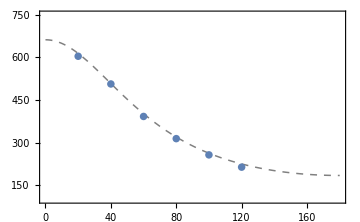

peakCompare.pdf

```mathematica
peakCompare=Show[
Plot[eFunction[toRad[x]],{x,0,180},
PlotTheme->"Scientific",
PlotRange->{{0,180},{100,750}},
ImagePadding->{{50,50},{28,30}},
ImageSize->Medium,
GridLines->None,
PlotStyle->Directive[Dashed,Gray,Thickness[.003]]],
ListPlot[{angleList,eList}ᵀ,
PlotStyle->PointSize[.015]],
Epilog->(Inset[MaTeX[#1],Scaled[#2]]&)@@@{
{"\\theta / \\si{\\deg}",{1.08,0}},
{"e / \\si{\\keV}",{0,1.08}}
},
PlotRangeClipping->False]
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@peakCompare
```

```mathematica
Import["data.xlsx"]⟦1⟧⟦All,7⟧
crossSectData=%⟦2;;⟧;
```

{rel,1.,0.642683,0.373969,0.25835,0.212835,0.203156}

```mathematica
crossSectionRel[θ_]:=(1/(1+α(1-Cos[θ])))^2((1+Cos[θ]^2)/2)(1+(α^2(1-Cos[θ])^2)/((1+Cos[θ]^2)(1+α(1-Cos[θ]))));
```

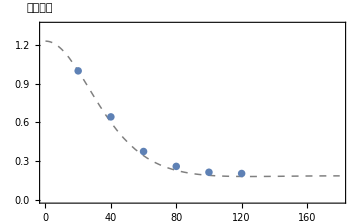

crossSectPlot.pdf

```mathematica
crossSectPlot=Show[
Plot[crossSectionRel[toRad[x]]/crossSectionRel[toRad[20]],{x,0,180},
PlotTheme->"Scientific",
PlotRange->{{0,180},{0,1.35}},
ImagePadding->{{50,50},{28,30}},
ImageSize->Medium,
GridLines->None,
PlotStyle->Directive[Dashed,Gray,Thickness[.003]]],
ListPlot[{angleList,crossSectData}ᵀ,
PlotStyle->PointSize[.015]],
Epilog->Append[(Inset[MaTeX[#1],Scaled[#2]]&)@@@{
{"\\theta / \\si{\\deg}",{1.08,0}}
},Inset["相对截面",Scaled[{0,1.08}]]],
PlotRangeClipping->False]
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@crossSectPlot
```